```mathematica
λ=0.614213*I;
soluciones=Solve[-2 (λ+λ^3)+(3+9 λ^2) z-12 λ z^2+(3+λ^2) z^3==0,z]
z1=z/.soluciones[[1]]
z2=z/.soluciones[[2]]
z3=z/.soluciones[[3]]
```

{{z→0.-0.283648 ⅈ},{z→0.+0.378726 ⅈ},{z→0.+2.71517 ⅈ}}

0.-0.283648 ⅈ

0.+0.378726 ⅈ

0.+2.71517 ⅈ

```mathematica
p[z_]:=(z^2-1)(z-λ);lp[z_]=p[z]p''[z]/p'[z]/p'[z];sp[z_]=z-1/(1-lp[z])p[z]/p'[z];
iterSch= Compile[{{z,_Complex}},sp[z]];
r1=1;r2=-1;r3=λ;
Clear[rootPosition]
rootPosition[z_]:= 
Which[Abs[z - r1] <  10.0^(-6), 3,
	       Abs[z - r2] <  10.0^(-6), 2,
	       Abs[z -r3] <  10.0^(-6), 1,
	       True, 0]
Clear[iterColorAlgorithm,colorLevel,fractalColor,plotColorFractal]
iterColorAlgorithm[iterMethod_,x_,y_,lim_] :=
Block[{z,ct,r}, z = x + y I; ct = 0;r = rootPosition[z];
While[(r==0) && (ct < lim),++ct;
z = iterMethod[z];r = rootPosition[z]
];
If[Head[r]==Which,r =0]; (* "Which" unevaluated *)
Return[N[r+ct/(lim+0.001)]]
]
colorLevelWS= Compile[{{p,_Real}},0.4*FractionalPart[p]];
fractalColorWS[p_] :=
Block[{pp = colorLevelWS[p]},
Switch[IntegerPart[p],
3, CMYKColor[0.6+pp,0.,0.,2*pp],
2, CMYKColor[0.,0.6+pp,0.,2*pp],
1, CMYKColor[0.,0.,0.6+pp,2*pp],
0, CMYKColor[0.,0.,0.,1.]
]
]
ft[min_,max_,pt_,nTicks_]:=Block[{taux,j,stepTicks=(max-min)/(nTicks-1)},
taux=Table[{pt*(j-1)/(nTicks-1)+1,min+(j-1)*stepTicks},{j,1,nTicks}]
]
plotColorFractal[iterMethod_,points_]:=
Block[{$Messages = {},
stepx=(xxMax-xxMin)/points,stepy=(yyMax-yyMin)/points},
ArrayPlot[Table[iterColorAlgorithm[iterMethod,x,y,limIterations],
{y,yyMax,1.00001*yyMin,-stepy},
{x,xxMin,1.00001*xxMax,stepx}],
FrameTicks->{ft[yyMax,yyMin,points,5],ft[xxMin,xxMax,points,5]},
PlotRange->{0,4},(* Three roots *)
ColorFunctionScaling->False,
ColorFunction->fractalColorWS
]
]
```

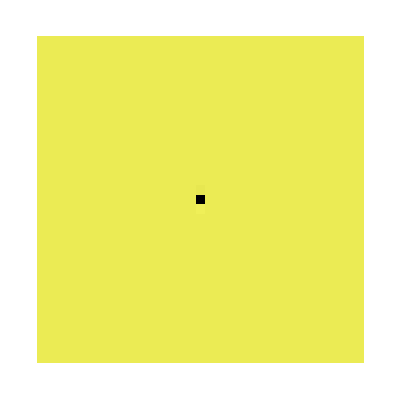

```mathematica
numberPoints =32;
limIterations=50;
xxMin=-300.; xxMax=300; yyMin=-300; yyMax=300;
plotColorFractal[iterSch, numberPoints]
```

```mathematica
numberPoints =512;
limIterations=50;
xxMin=Re[z3]-1; xxMax=Re[z3]+1; yyMin=Im[z3]-1; yyMax=Im[z3]+2.75;
plotColorFractal[iterSch, numberPoints]
```

-Graphics-

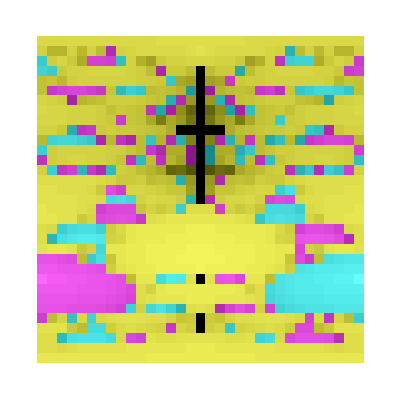

```mathematica
numberPoints =32;
limIterations=50;
xxMin=-1; xxMax=1; yyMin=-2; yyMax=6;
plotColorFractal[iterSch, numberPoints]
```

```mathematica
NestList[sp,z1,100]
```

{0.-0.283648 ⅈ,0.-5.1766 ⅈ,0.+0.467053 ⅈ,0.+0.600655 ⅈ,0.+0.614052 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ}

```mathematica
NestList[sp,z2,100]
```

{0.+0.378726 ⅈ,0.+0.593051 ⅈ,0.+0.613827 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ,0.+0.614213 ⅈ}

```mathematica
NestList[sp,z3,10000]
```

```mathematica
NestList[sp,-17/2*I,100]
```

{-(17 ⅈ)/2,0.+0.473137 ⅈ,0.+1.21244 ⅈ,0.-5.11115 ⅈ,0.+0.502294 ⅈ,0.+1.33623 ⅈ,0.-3.36606 ⅈ,0.+0.700725 ⅈ,0.+2.73825 ⅈ,0.-0.80203 ⅈ,0.-4.52344 ⅈ,0.+0.542574 ⅈ,0.+1.52957 ⅈ,0.-2.25331 ⅈ,0.+1.13582 ⅈ,0.-7.76285 ⅈ,0.+0.46118 ⅈ,0.+1.16499 ⅈ,0.-6.46501 ⅈ,0.+0.460623 ⅈ,0.+1.16282 ⅈ,0.-6.54561 ⅈ,0.+0.459722 ⅈ,0.+1.15932 ⅈ,0.-6.68009 ⅈ,0.+0.458533 ⅈ,0.+1.15472 ⅈ,0.-6.86648 ⅈ,0.+0.457497 ⅈ,0.+1.15072 ⅈ,0.-7.03735 ⅈ,0.+0.457137 ⅈ,0.+1.14934 ⅈ,0.-7.0987 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09838 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ}

```mathematica
lista={0.+2.6489948711008 ⅈ,0.-0.03849509180007793 ⅈ,0.+4.4793440350024945 ⅈ,0.+0.004799055127977958 ⅈ,0.+2.35961871854149 ⅈ,0.-0.031832564428404986 ⅈ,0.+3.9768490644366477 ⅈ,0.-0.010032519359232328 ⅈ,0.+2.851663078644589 ⅈ,0.-0.03800140887123726 ⅈ,0.+4.4384854381740535 ⅈ,0.+0.0036244391859794334 ⅈ,0.+2.3931832268987416 ⅈ,0.-0.033224687490717386 ⅈ,0.+4.073699797387601 ⅈ,0.-0.007125480526339878 ⅈ,0.+2.7422378608125064 ⅈ,0.-0.03865278681489448 ⅈ,0.+4.4925302795888165 ⅈ,0.+0.005176615720656308 ⅈ,0.+2.348999674027782 ⅈ,0.-0.03135014924785029 ⅈ,0.+3.944192586654596 ⅈ,0.-0.011014389578968053 ⅈ,0.+2.89029686986229 ⅈ,0.-0.03759310246544523 ⅈ,0.+4.405169034649607 ⅈ,0.+0.0026615185670069152 ⅈ,0.+2.4213087829778783 ⅈ,0.-0.03424413507572188 ⅈ,0.+4.14718659496738 ⅈ,0.-0.004929370256085974 ⅈ,0.+2.664185100514572 ⅈ,0.-0.03857230709865922 ⅈ,0.+4.485792438566465 ⅈ,0.+0.004983785808590824 ⅈ,0.+2.3544129080593152 ⅈ,0.-0.03159866330377126 ⅈ,0.+3.960958533272096 ⅈ,0.-0.010510250937938892 ⅈ,0.+2.870350977361379 ⅈ,0.-0.037814379777989515 ⅈ,0.+4.423171542624519 ⅈ,0.+0.0031823936845540857 ⅈ,0.+2.406025452673556 ⅈ,0.-0.033706235837235976 ⅈ,0.+4.108134924026311 ⅈ,0.-0.006095071823540188 ⅈ,0.+2.7051414031418153 ⅈ,0.-0.038677740538948235 ⅈ,0.+4.494622926372715 ⅈ,0.+0.005236464868738189 ⅈ,0.+2.3473238602925304 ⅈ,0.-0.03127211095146443 ⅈ,0.+3.9389525009802218 ⅈ,0.-0.011171963787508954 ⅈ,0.+2.8965791629857276 ⅈ,0.-0.03751893919884175 ⅈ,0.+4.399163154652078 ⅈ,0.+0.0024874582846985405 ⅈ,0.+2.426452796300518 ⅈ,0.-0.03441679102774442 ⅈ,0.+4.159855032316775 ⅈ,0.-0.004551950912734526 ⅈ,0.+2.651148673684473 ⅈ,0.-0.038507347440034145 ⅈ,0.+4.4803664751848595 ⅈ,0.+0.004828357462683286 ⅈ,0.+2.358791656449104 ⅈ,0.-0.03179573492917642 ⅈ,0.+3.9743398324935924 ⅈ,0.-0.010107949064708244 ⅈ,0.+2.8546000771692017 ⅈ,0.-0.03797335267045776 ⅈ,0.+4.436182462840186 ⅈ,0.+0.0035580239967449856 ⅈ,0.+2.3951052633249366 ⅈ,0.-0.0332985105541308 ⅈ,0.+4.078947036582476 ⅈ,0.-0.0069683310511177154 ⅈ,0.+2.736524876507078 ⅈ,0.-0.03866367918794289 ⅈ,0.+4.493443522159827 ⅈ,0.+0.005202736566281452 ⅈ,0.+2.348268023562825 ⅈ,0.-0.031316142675883896 ⅈ,0.+3.9419076776875315 ⅈ,0.-0.011083098660739754 ⅈ,0.+2.893033390828907 ⅈ,0.-0.037561055878256866 ⅈ,0.+4.4025721338346555 ⅈ,0.+0.0025862737313344653 ⅈ,0.+2.423530223067244 ⅈ,0.-0.034319207969961685 ⅈ,0.+4.15268693949497 ⅈ,0.-0.004765456568719628 ⅈ,0.+2.658510085533527 ⅈ,0.-0.038545959908558025 ⅈ,0.+4.483590358887861 ⅈ,0.+0.004920721917653914 ⅈ,0.+2.3561878835239503 ⅈ,0.-0.031678972081152335 ⅈ,0.+3.966402339598545 ⅈ,0.-0.01034657684977125 ⅈ,0.+2.8639251781113053 ⅈ,0.-0.037880950514274314 ⅈ,0.+4.428612031185683 ⅈ,0.+0.0033395471930228737 ⅈ,0.+2.40144646783016 ⅈ,0.-0.03353767972260702 ⅈ,0.+4.096025710973811 ⅈ,0.-0.006457171540790618 ⅈ,0.+2.718080538924633 ⅈ,0.-0.038681503012854 ⅈ,0.+4.494938595404419 ⅈ,0.+0.005245491262058977 ⅈ,0.+2.3470712922259653 ⅈ,0.-0.031260304001782924 ⅈ,0.+3.9381607179596188 ⅈ,0.-0.011195773560610522 ⅈ,0.+2.8975304318601496 ⅈ,0.-0.03750752676493452 ⅈ,0.+4.398240189508701 ⅈ,0.+0.00246069652834624 ⅈ,0.+2.4272453341807445 ⅈ,0.-0.034443022480502794 ⅈ,0.+4.16178547532172 ⅈ,0.-0.004494472832879737 ⅈ,0.+2.6491727841965496 ⅈ,0.-0.03849612072484909 ⅈ,0.+4.479429858920789 ⅈ,0.+0.004801514947411434 ⅈ,0.+2.359549270855389 ⅈ,0.-0.03182947667845237 ⅈ,0.+3.9766385899027803 ⅈ,0.-0.010038846281583691 ⅈ,0.+2.851909233540853 ⅈ,0.-0.0379990768623375 ⅈ,0.+4.438293939286023 ⅈ,0.+0.0036189174126270984 ⅈ,0.+2.3933429254872367 ⅈ,0.-0.03323084503371909 ⅈ,0.+4.07413702978644 ⅈ,0.-0.007112384120981474 ⅈ,0.+2.741760987631888 ⅈ,0.-0.0386537914324081 ⅈ,0.+4.492614495905794 ⅈ,0.+0.005179024653839015 ⅈ,0.+2.3489321830526855 ⅈ,0.-0.03134701649701377 ⅈ,0.+3.9439820027730996 ⅈ,0.-0.011020721988161064 ⅈ,0.+2.890548892226955 ⅈ,0.-0.03759016786061142 ⅈ,0.+4.404931120187944 ⅈ,0.+0.002654626148648198 ⅈ,0.+2.4215121227316825 ⅈ,0.-0.034251039330963184 ⅈ,0.+4.147691931445985 ⅈ,0.-0.004914307957370134 ⅈ,0.+2.663662760213385 ⅈ,0.-0.03857000526453369 ⅈ,0.+4.4855999795675885 ⅈ,0.+0.004978274940756755 ⅈ,0.+2.3545679243749387 ⅈ,0.-0.03160570010478292 ⅈ,0.+3.961435024112582 ⅈ,0.-0.010495924292207803 ⅈ,0.+2.869787546805878 ⅈ,0.-0.037820310301700744 ⅈ,0.+4.423655753275044 ⅈ,0.+0.003196385455288109 ⅈ,0.+2.405617172712942 ⅈ,0.-0.0336913468685629 ⅈ,0.+4.107062847522737 ⅈ,0.-0.0061271185153382035 ⅈ,0.+2.706282348541417 ⅈ,0.-0.038678624232908465 ⅈ,0.+4.4946970643141935 ⅈ,0.+0.0052385848440543725 ⅈ,0.+2.3472645369758034 ⅈ,0.-0.03126933880167071 ⅈ,0.+3.938766574321779 ⅈ,0.-0.011177554801919953 ⅈ,0.+2.896802492779302 ⅈ,0.-0.03751626418825582 ⅈ,0.+4.398946787267768 ⅈ,0.+0.0024811849258963292 ⅈ,0.+2.426638539680757 ⅈ,0.-0.034422947589534125 ⅈ,0.+4.160307973904916 ⅈ,0.-0.0045384639622447764 ⅈ,0.+2.650684817261112 ⅈ,0.-0.03850474486782751 ⅈ,0.+4.480149319561961 ⅈ,0.+0.004822134329430128 ⅈ,0.+2.3589672639087382 ⅈ,0.-0.03180356524136663 ⅈ,0.+3.974873095521146 ⅈ,0.-0.01009191844127022 ⅈ,0.+2.853975467754905 ⅈ,0.-0.0379793616614692 ⅈ,0.+4.436675536093386 ⅈ,0.+0.003572245514320116 ⅈ,0.+2.39469347598526 ⅈ,0.-0.03328274665900244 ⅈ,0.+4.077825600366753 ⅈ,0.-0.007001913068227061 ⅈ,0.+2.737744022212725 ⅈ,0.-0.038661564763090794 ⅈ,0.+4.493266219035979 ⅈ,0.+0.005197665572008958 ⅈ,0.+2.3484100328482387 ⅈ,0.-0.03132275097327586 ⅈ,0.+3.942351515335959 ⅈ,0.-0.011069752064461813 ⅈ,0.+2.892501485584879 ⅈ,0.-0.037567316191986944 ⅈ,0.+4.403079234991125 ⅈ,0.+0.0026009690286850073 ⅈ,0.+2.4230961044489026 ⅈ,0.-0.034304598346292625 ⅈ,0.+4.151615571808222 ⅈ,0.-0.004797378405889674 ⅈ,0.+2.65961367978905 ⅈ,0.-0.038551315209268466 ⅈ,0.+4.484037802297012 ⅈ,0.+0.004933537649314701 ⅈ,0.+2.3558269918329513 ⅈ,0.-0.031662690407241456 ⅈ,0.+3.9652976483825246 ⅈ,0.-0.010379789730385003 ⅈ,0.+2.8652271438305648 ⅈ,0.-0.03786765164331074 ⅈ,0.+4.427524273191013 ⅈ,0.+0.003308135987769134 ⅈ,0.+2.402360512001227 ⅈ,0.-0.03357160280251259 ⅈ,0.+4.098457910191 ⅈ,0.-0.006384419497396543 ⅈ,0.+2.715472465417529 ⅈ,0.-0.03868184156595866 ⅈ,0.+4.494967001631386 ⅈ,0.+0.005246303502153715 ⅈ,0.+2.3470485671546886 ⅈ,0.-0.031259241073931854 ⅈ,0.+3.9380894504182726 ⅈ,0.-0.011197916653563844 ⅈ,0.+2.897616080418332 ⅈ,0.-0.03750649689089203 ⅈ,0.+4.398156916023874 ⅈ,0.+0.002458281813133567 ⅈ,0.+2.427316866552634 ⅈ,0.-0.03444538522791474 ⅈ,0.+4.161959430784805 ⅈ,0.-0.004489293834065933 ⅈ,0.+2.6489948711009497 ⅈ};
```

```mathematica
Length[lista]
```

257

```mathematica
Log[2,256]
```

8